Last modified on: Tuesday, July 10, 2018 at 16:34

Author Info

Luis Antonio Vasquez Reina

Jonathan Gorard

Pontifical Catholic University of Peru - PUCP

Poster Session Content

A Calculus for Infinite Lists

Computer languages are usually constrained to lists of finite size subjected to operations. For example, one may join, partition, sum, or nest them, and get a finite list as a result. Even though explicit infinite lists cannot be implemented in a computer, in this project I aim to provide the Wolfram Language with a symbolic calculus for lists of infinite length.
That is, one would be able to treat expressions referring to infinite lists as arguments of operations, e.g, the infinite list of the roots of the natural numbers. The implementation of this kind of operation to the Wolfram Language is the objective of my project.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics--Graphics-

I have extended most of the basic Mathematica functions for lists to infinite lists through symbolic manipulation, though partial explicit numerical results can be obtained.
Two non trivial applications of this results are the capacity to define infinite graphs, and to work with Cellular Automata with an infinite initial condition.

It is still pendant to extend other Mathematica functions for finite lists to work with this project’s approach for infinite lists in an optimal way. Also, an implementation could be explored for systems that in principle accept infinite initial conditions.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Basic Operations with Infinite Lists

Many of the basic operations on lists now have a version for infinite lists!

First, I define the infinite list of the cubes of the integers

cubes=InfiniteList[0,x↦x^3];
(*showing the first five element on both sides*)
InfinitePrint[cubes]

{...,-125,-64,-27,-8,-1,0,1,8,27,64,125,...}

One can reverse this list, or drop all the negative cubes.

InfiniteReverse[cubes]//InfinitePrint
InfiniteDrop[cubes,{-Infinity,-1}]//InfinitePrint

{...,125,64,27,8,1,0,-1,-8,-27,-64,-125,...}
{1,8,27,64,125,...}

Here, I make the range from 1 to infinity, and select all the primes:

InfiniteSelect[ InfiniteRange[1,Infinity],PrimeQ] //InfinitePrint

{2,3,5,7,11,...}

Matrices and graphs

With the help of infinite lists, it is possible to work with matrices, which are nested infinite lists.

myInfiniteMatrix=
InfiniteMatrix[{i,j}↦"[row "<>ToString[i]<>",col "<>ToString[j]<>"]"];
(*Take the first rows and columns*)
InfiniteTake[myInfiniteMatrix,2,3]//MatrixForm
InfiniteTake[myInfiniteMatrix,4,4]//MatrixForm

("[row 1,col 1]" | "[row 1,col 2]" | "[row 1,col 3]"
"[row 2,col 1]" | "[row 2,col 2]" | "[row 2,col 3]")

("[row 1,col 1]" | "[row 1,col 2]" | "[row 1,col 3]" | "[row 1,col 4]"
"[row 2,col 1]" | "[row 2,col 2]" | "[row 2,col 3]" | "[row 2,col 4]"
"[row 3,col 1]" | "[row 3,col 2]" | "[row 3,col 3]" | "[row 3,col 4]"
"[row 4,col 1]" | "[row 4,col 2]" | "[row 4,col 3]" | "[row 4,col 4]")

Infinite matrices allow us to work with infinite graphs!
We can consider the graph with vertices the natural numbers, and where every number is connected its divisors

myGraphMatrix=InfiniteMatrix[{x,y}↦If[Mod[x,y]==0,1,0]];
Table[GraphPlot[ 
InfiniteTake[myGraphMatrix,n,n],
VertexLabeling→True,DirectedEdges→True],
{n,4,9}]

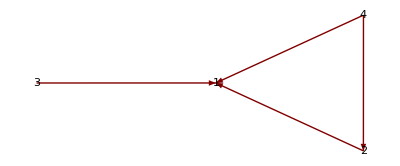
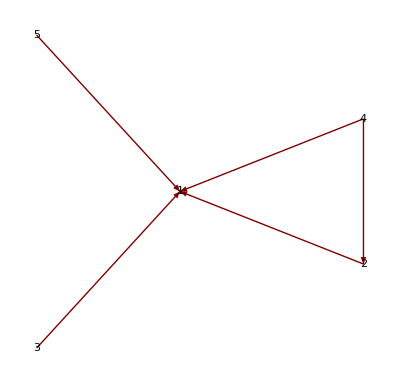
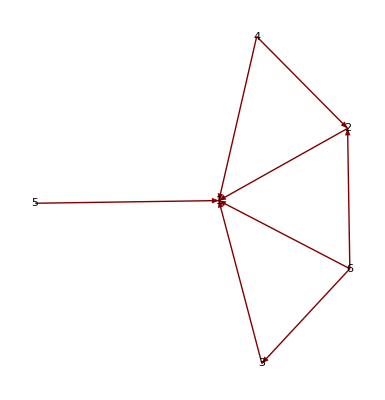
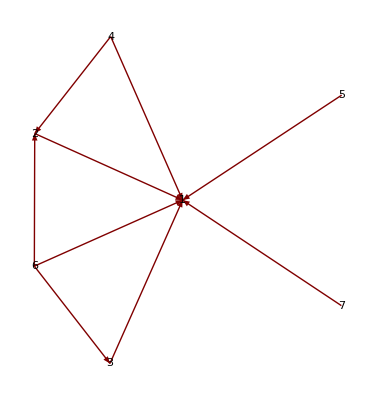
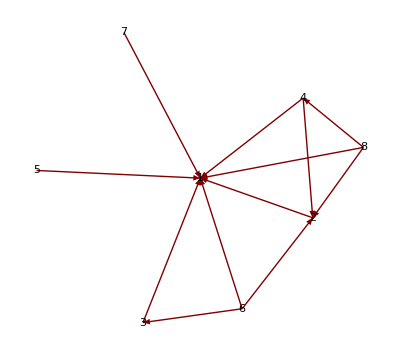
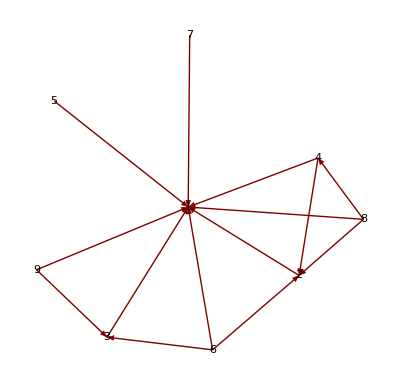

Applications to Cellular Automata

A neat application is that now we can have Cellular Automata that admit infinite initial conditions!
For example, rule 90 gives interesting results:

(*Initial condition with a black cell every 7 cells*)
myInitialCondition=InfiniteList[0,x↦If[Mod[x,7]==0,1,0]];
(*With a widht of 40 cells to either side, plot the first 10 steps*)
InfiniteCellularAutomatonPlot1[90,myInitialCondition,40,10]

-Graphics-

Or we can see rule 90 where only the cells in prime number position are black:

-Graphics-

There are differences if one uses the implemented Cellular Automata function with a similar but finite initial condition. Notice the extremes of the images below.

(*with infinite initial condition*)
-Graphics-
(*with finite initial condition*)
-Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

If the InfiniteLists.m package is in the same folder as the current notebook, one can load the package with the following command:

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"InfiniteLists.m"}]]
```

General Introduction

Main idea: Infinite lists are treated as symbolical objects within the Wolfram Language. All infinite lists are countably infinite. An infinite list consists of two components, a direction and a rule that generates its elements. Elements can be of any Head.
With this approach, one can think of the infinite list as “lazily” implemented, i.e,  values are only computed when explicitly asked for. 
By far, the most complicated part of the project was to figure out the constructions needed for the generating rules for the new infinite lists that result from manipulating (applying functions) to infinite lists.
Note that, thanks to functions that insert a finite amount of elements to the list, strictly speaking the generating rule is only needed for the elements in the tail of the infinite list.
After the basic implementation was completed, infinite matrices were quickly available, via nesting of infinite lists and some modification of the already implemented functions of the project. With this,  the implementation of graphs with an infinite number of nodes and infinite adjacent matrices was possible. 
1- dimensional Cellular Automata with infinite initial conditions become available. Though the implementation here is still inefficient, it respects the spirit of cellular automata, which is that the value of a cell depends locally on the cells above it.

Technical Introduction

Infinite lists are objects: InfiniteList[direction,rule].
There are three types of infinite lists:
direction 1 lists  : open on the right side, closed on the left side. 	Example: {1,2,3,4,5,....}
direction -1 lists: open on the left side, closed on the right side. 	Example: {....,-5,-4,-3,-2,-1}
direction 0 lists  : open on both sides: 						Example: {...,-3,-2,-1,0,1,2,---}

Most functions take one or more infinite lists as input and return an infinite list as output. Some of these operations change the direction and most of them change the generating rule.

List of all functions and objects implemented:
(Still inefficient implementations are marked with “ * ”. A “-” is added for ease of reading, but is not included in the name of the function or object )

Infinite-List
Infinite-Prepend
Infinite-Append
Infinite-Part
Infinite-Take
Infinite-Length
Infinite-Print
Infinite-Drop
Infinite-First
Infinite-Last
Infinite-Direction
Infinite-Range
Infinite-Reverse
Infinite-Join
Infinite-RealDigits*
Infinite-Rest
Infinite-Most
Infinite-Riffle
Infinite-SelectRule
Infinite-Select*
Infinite-Cases*
Infinite-Rule
Infinite-FirstPosition
Infinite-Unequal
Infinite-Plus
Infinite-Times
Infinite-Sum
Infinite-Unequal*
Infinite-And
Infinite-And2*
Infinite-Or
Infinite-Matrix
Infinite-MatrixPlus
Infinite-MatrixTimes
Infinite-PolyTimes
Infinite-CellularAutomatonStep*
Infinite-CellularAutomaton
Infinite-CellularAutomatonData1*
Infinite-CellularAutomatonPlot1*
Infinite-CellularAutomatonData2
Infinite-CellularAutomatonPlot2

A lot of functions return a Failure object if they are called with the wrong arguments, specifically:
InfinitePrepend, InfiniteAppend, InfinitePart, InfiniteTake, InfiniteDrop, InfiniteFirst, InfiniteLast, InfiniteJoin, InfiniteRest, InfiniteMost, InfiniteEqual

#### Code

Provide one of:

Link to the GitHub: https://github.com/LuisAVasquez/Summer2018Starter

see under “project-notebooks” folder for the progressive advance of the project: https://github.com/LuisAVasquez/Summer2018Starter/tree/master/Project%20Notebooks

The package “Infinite Lists” includes the code for all the functions implemented in this project

For the sake of completeness, I’ll include the code of my InfiniteLists Package, which has explanations of the inner structure of the functions

```mathematica
BeginPackage["InfiniteLists`"]

(*There are three types of infinite lists:
direction 1 lists  : open on the right side, closed on the left side. 	Example: {1,2,3,4,5,....}
direction -1 lists: open on the left side, closed on the right side. 	Example: {....,-5,-4,-3,-2,-1}
direction 0 lists  : open on both sides:						Example: {...,-3,-2,-1,0,1,2,---}*)
InfiniteList[direction_,rule_][n_Integer]:= rule@n /;((direction==0)||(direction*n>0))
InfiniteList[direction_,rule_][n_Integer]:=
Failure["InvalidInfinitePart",<|"MessageTemplate"->"Invalid infinite part specification"|>]/;Not@((direction==0)||(direction*n>0))
```

```mathematica
(*Attention: Most of the functions are analogous to the ones already in the Wolfram Language, 
and they have "Infinite" added before the existing name*)

(*Prepend only works for direction 1*)
InfinitePrepend[InfiniteList[direction_,rule_],elem_]:=
With[{newrule= If[#==1,elem,rule@(#-1)]&
}, InfiniteList[direction,newrule]]/;(direction==1 );

InfinitePrepend[InfiniteList[direction_,rule_],elem_]:=
Failure["InvalidInfinitePrepend",<|"MessageTemplate"->"InfinitePrepend only defined for right-open infinite lists"|>]/;(direction!= 1 );
```

```mathematica
(*Append only works for direction -1*)
InfiniteAppend[InfiniteList[direction_,rule_],elem_]:=
With[{newrule= If[#==-1,elem,rule@(#+1)]&
}, InfiniteList[direction,newrule]]/;(direction==-1 );

InfiniteAppend[InfiniteList[direction_,rule_],elem_]:=
Failure["InvalidInfinitePrepend",<|"MessageTemplate"->"InfinitePrepend only defined for left-open infinite lists"|>]/;(direction!= -1 );
```

```mathematica
InfinitePart[InfiniteList[direction_,rule_],n_Integer]:=rule@n /;((direction==0)||(direction*n>0));

InfinitePart[InfiniteList[direction_,rule_],n_Integer]:=
Failure["InvalidInfinitePart",<|"MessageTemplate"->"Invalid infinite part specification"|>]/;Not@((direction==0)||(direction*n>0))
```

```mathematica
(*only integers can be taken as indexs!*)
InfinitePart[InfiniteList[direction_,rule_],list_List/;AllTrue[list,IntegerQ]]:=
InfinitePart[InfiniteList[direction,rule],list]=Map[rule,list]
InfinitePart[InfiniteList[direction_,rule_],list_List]:=Failure/;!AllTrue[list,IntegerQ]
(*this definitions needs to be refined! *)
```

```mathematica
(*Infinite Take, based on InfinitePart*)
InfiniteTake[InfiniteList[direction_,rule_],n_Integer]:=InfinitePart[InfiniteList[direction,rule],Range[n]]/;(direction==1&&n>0);
InfiniteTake[InfiniteList[direction_,rule_],n_Integer]:=InfinitePart[InfiniteList[direction,rule],Range[-1,n,-1]]/;(direction==-1 &&n<0);
(* for direction -1 lists, InfiniteTake[#,n] returns in the order {-1,-2,-3,...,-Abs[n]}  *)

InfiniteTake[InfiniteList[direction_,rule_],n_Integer]:=Failure/;Not@Or[(direction==1&&n>0),(direction==-1 &&n<0)]
InfiniteTake[InfiniteList[direction_,rule_],{n_Integer,m_Integer}]:= InfinitePart[InfiniteList[direction,rule],Range[n,m,1]]/;
(direction==1&& n<=  m);

InfiniteTake[InfiniteList[direction_,rule_],{n_Integer,m_Integer}]:= InfinitePart[InfiniteList[direction,rule],Range[n,m,-1]]/;
(direction==-1&&m<=n<0);
 (*careful with the direction of the part in direction -1 lists!!*) 
(*InfiniteTake[mIL, {-4,-8}] = {mIL⟦-4⟧,mIL⟦-5⟧,...,mIL⟦-8⟧}  *) (*mIL is an arbitrary direction -1 infinite list*)
(*with this implementation we have:     InfiniteTake[mIL,{-1,-Abs[n]}]= InfiniteTake[mIL,-Abs[n]]  *)
InfiniteTake[InfiniteList[direction_,rule_],{n_Integer,m_Integer}]:= InfinitePart[InfiniteList[direction,rule],Range[n,m,1]]/;
(direction==0&&  n<=m );
InfiniteTake[InfiniteList[direction_,rule_],{n_Integer,m_Integer}]:=
Failure/; Not@Or[(direction==1&& n<=  m),(direction==-1&&m<=n<0),(direction==0&&  n<=m )];

(*beginning work of the 04.07 for this definition*)
InfiniteTake[InfiniteList[direction_,rule_],{n_Integer,Infinity}]:=
With[{newrule=rule@(#+n-1)&},InfiniteList[direction,newrule]]/;(direction==1&&n>0);
InfiniteTake[InfiniteList[direction_,rule_],{n_Integer,Infinity}]:=Failure/;Not@(direction==1&&n>0||direction==0);	
InfiniteTake[InfiniteList[direction_,rule_],{-Infinity,n_Integer}]:=
With[{newrule=rule@(#+n+1)&},InfiniteList[direction,newrule]]/;(direction==-1&&n<0);
InfiniteTake[InfiniteList[direction_,rule_],{-Infinity,n_Integer}]:=Failure/;Not@(direction==-1&&n<0||direction==0);

InfiniteTake[InfiniteList[direction_,rule_],{-Infinity,Infinity}]:=InfiniteList[direction,rule]/;direction==0;
InfiniteTake[InfiniteList[direction_,rule_],{-Infinity,Infinity}]:=Failure/;Not@direction==0;		
(*notice that direction 0 lists can get direction 1 or -1 lists taken from them!*)
InfiniteTake[InfiniteList[0,rule_],{n_Integer,Infinity}]:=
	With[{newrule=rule@(#+n-1)&},InfiniteList[1,newrule]];
InfiniteTake[InfiniteList[0,rule_],{-Infinity,n_Integer}]:=
	With[{newrule=rule@(#+n+1)&},InfiniteList[-1,newrule]];
(*end of work of the 04.07 for this definition*)
```

```mathematica
InfiniteLength[InfiniteList[direction_,rule_]]=Infinity; (*by far the easiest*)
```

```mathematica
(*InfinitePrint*)
(*This shows some elements of the infnite list*)
InfinitePrint[InfiniteList[0,rule_],n_:5]:=
Print[Join[{"..."},InfiniteTake[InfiniteList[0,rule],{-n,n}],{"..."}]]
InfinitePrint[InfiniteList[1,rule_],n_:5]:=
Print[Join[InfiniteTake[InfiniteList[1,rule],n],{"..."}]]
InfinitePrint[InfiniteList[-1,rule_],n_:-5]:=
Print[Join[{"..."},Reverse[InfiniteTake[InfiniteList[-1,rule],n]]]]
 (*the Reverse is here because of how infiniteTake works for -1 lists*)
```

```mathematica
(*InfiniteDrop*)
InfiniteDrop[InfiniteList[direction_,rule_],n_Integer]:=
	With[{newrule= rule@(#+n)&},
	InfiniteList[direction,newrule]
]/;(direction==1 &&n>0);
InfiniteDrop[InfiniteList[direction_,rule_],n_Integer]:=
	With[{newrule= rule@(#+n)&}, (*"+n" even though n<0 *)
	InfiniteList[direction,newrule]
]/;(direction==-1 &&n<0);
InfiniteDrop[InfiniteList[direction_,rule_],n_Integer]:=Failure/; Not@Or[(direction==1 &&n>0),(direction==-1 &&n<0)]
InfiniteDrop[InfiniteList[direction_,rule_],{n_Integer}]:=
	With[{newrule=(If[#<n,rule@#, rule@(#+1)])&},
	InfiniteList[direction,newrule]]/;(direction==1&&n>0);
InfiniteDrop[InfiniteList[direction_,rule_],{n_Integer}]:=
	With[{newrule=(If[#>n,rule@#, rule@(#-1)])&},
	InfiniteList[direction,newrule]]/;(direction==-1&&n<0);
(*beginning work of the 05.07 on this definition*)
InfiniteDrop[InfiniteList[direction_,rule_],{n_Integer,m_Integer}]:=
	With[{newrule=If[#<n,rule@#,rule@(#+m-n+1)]&},
		InfiniteList[direction,newrule]]/;(direction==1&&0<n<=m);
InfiniteDrop[InfiniteList[direction_,rule_],{n_Integer,m_Integer}]:=
	With[{newrule=If[#>n,rule@#,rule@(#+m-n-1)]&},
InfiniteList[direction,newrule]]/;(direction==-1&&m<=n<0);

InfiniteDrop[InfiniteList[direction_,rule_],{n_Integer,m_Integer}]:=
(*problems if range includes index 0*)
Module[{newrule},
	newrule=Which[ n>0,If[#<n,rule@#,rule@(#+m-n+1)]&,
				   m<0,If[#>m,rule@#,rule@(#+n-m-1)]&,
				True,If[#>=0,rule@(#+m+1),rule@(#+n)]&] ;
(*remember n<0 in this case*)
InfiniteList[direction,newrule] ]/;(direction==0&&n<=m);

InfiniteDrop[InfiniteList[direction_,rule_],{n_Integer,m_Integer}]:=
Failure/;Not@Or[(direction==1&&0<n<=m),(direction==-1&&m<=n<0),(direction==0&&n<=m)];

InfiniteDrop[InfiniteList[direction_,rule_],{n_Integer,Infinity}]:=
If[direction==1&&n==1,{},InfiniteTake[InfiniteList[direction,rule],n-1]]/;(direction==1&&n>0)
InfiniteDrop[InfiniteList[direction_,rule_],{n_Integer,Infinity}]:=
With[{newrule=rule@(#+n)&}, InfiniteList[-1,newrule]]/;direction==0
InfiniteDrop[InfiniteList[direction_,rule_],{n_Integer,Infinity}]:=Failure/;Not@Or[direction==0,(direction==1&&n>0)]
InfiniteDrop[InfiniteList[direction_,rule_],{-Infinity,n_Integer}]:=
If[direction==-1&&n==-1,{},Reverse@InfiniteTake[InfiniteList[direction,rule],n+1]]/;(direction==-1&&n<0) (*remember the Reverse!*)
InfiniteDrop[InfiniteList[direction_,rule_],{-Infinity,n_Integer}]:=
With[{newrule=rule@(#+n)&},InfiniteList[1,rule]]/;direction==0
InfiniteDrop[InfiniteList[direction_,rule_],{-Infinity,n_Integer}]:=Failure/;Not@Or[direction==0,(direction==-1&&n<0)]
InfiniteDrop[InfiniteList[direction_,rule_],{-Infinity,Infinity}]:={}/;direction==0
InfiniteDrop[InfiniteList[direction_,rule_],{-Infinity,Infinity}]:=Failure/;direction!=0
(*end of work of 05.07 on this definition*)
```

```mathematica
(*First only makes sense for direction 1 lists*)
InfiniteFirst[InfiniteList[direction_,rule_]]:=rule@1/;direction==1
InfiniteFirst[InfiniteList[direction_,rule_]]:=Failure/;direction!=1

(*last only makes sense for direction -1 lists*)
InfiniteLast[InfiniteList[direction_,rule_]]:=rule@(-1)/;direction==-1
InfiniteLast[InfiniteList[direction_,rule_]]:=Failure/;direction!= -1
(*InfiniteDirection returns the direction of the list*)
InfiniteDirection[InfiniteList[direction_,rule_]]:=direction;

(*InfiniteRange, Infinite Reverse*)
InfiniteRange[n_Integer,Infinity]:=InfiniteList[1,x↦x+n-1];
InfiniteRange[-Infinity,n_Integer]:=InfiniteList[-1,x↦x+n+1];
InfiniteRange[-Infinity,Infinity]:=InfiniteList[0,x↦x];

InfiniteReverse[InfiniteList[direction_,rule_]]:=
With[{newrule=rule@(-#)&},InfiniteList[-direction,newrule]]
```

```mathematica
(*Infinite Join*)
InfiniteJoin[list_List,InfiniteList[direction_,rule_]]:=
With[{newrule=If[#<= Length[list],list[[#]],rule@(#-Length[list])]&},
InfiniteList[direction,newrule]]/;direction==1
InfiniteJoin[list_List,InfiniteList[direction_,rule_]]:=Failure/;Not@direction==1

InfiniteJoin[InfiniteList[direction1_,rule1_],InfiniteList[direction2_,rule2_]]:=
With[{newrule=If[#<0,rule1@#,rule2@(#+1)]&},
InfiniteList[0,newrule]]/;(direction1==-1&&direction2==1)
InfiniteJoin[InfiniteList[direction1_,rule1_],InfiniteList[direction2_,rule2_]]:= Failure/;Not@(direction1==-1&&direction2==1)
InfiniteJoin[InfiniteList[direction_,rule_],list_List]:=
With[{newrule= If[#>=-Length[list],list[[#]],rule@(#+Length[list]) ]&},
InfiniteList[direction,newrule]]/;direction==-1   
(*attention to the order:   Join[{...-3,-2,-1} ,{a,b,c,d}] ={...,-3,-2,-1,a,b,c,d} . NOT {...,-3,-2,-1,d,c,b,a} *) 
(*think of it as pasting one after the other*)
InfiniteJoin[InfiniteList[direction_,rule_],list_List]:=Failure/;direction!=-1
```

```mathematica
(*InfiniteRealDigits*)
(*this one seems very inefficient*)
(*returns a list of two elements: First the infinite list of the digits, Second the number of digits to the left of the decimal point*)
InfiniteRealDigits[x_/;x∈Reals,b_:10]:=
With[{rule= Last@First@RealDigits[x,b,#]&},
{InfiniteList[1,rule],RealDigits[x,b,Length[IntegerDigits@Floor[x]]][[2]]}]
InfiniteRealDigits[E][[1]] //InfiniteTake[#,10]&//AbsoluteTiming (*before modification*)
{0.0008095322421513319,{2,7,1,8,2,8,1,8,2,8}}
InfiniteRealDigits[E][[1]] //InfiniteTake[#,10]&//AbsoluteTiming (*after modification*)
{0.00012648941283614561,{2,7,1,8,2,8,1,8,2,8}}
InfiniteRealDigits[E,2][[2]]
2
```

```mathematica
(*InfiniteRest, InfiniteMost *)
(*Rest only makes sense for direction 1 lists*)
InfiniteRest[InfiniteList[direction_,rule_]]:=With[{newrule=rule@(#+1)&},InfiniteList[direction,newrule]]/;direction==1;
InfiniteRest[InfiniteList[direction_,rule_]]:=Failure/;direction!= 1;
(*Most only makes sense for direction -1 lists*)
InfiniteMost[InfiniteList[direction_,rule_]]:=With[{newrule=rule@(#-1)&},InfiniteList[direction,newrule]]/;direction==-1
InfiniteMost[InfiniteList[direction_,rule_]]:=Failure/;direction!= -1
```

```mathematica
(*InfiniteRiffle*)
InfiniteRiffle[InfiniteList[direction_,rule_],x_]:=
With[{newrule=If[Mod[direction*#,2]==1,rule@((#+direction)/2),x]&
 (*#+direction: I use this not to write #+1 for direction 1 lists or #-1 for -1 lists*)
},InfiniteList[direction,newrule]]/;(direction==1||direction==-1)
InfiniteRiffle[InfiniteList[direction_,rule_],x_]:=
With[{newrule=If[Mod[#,2]==1,x,rule@(#/2)]&},InfiniteList[direction,newrule]]/;direction==0
```

```mathematica
(*InfiniteSelectRule, InfiniteSelect*)

(*First I'm implementing a way to get the nth element that satisfies an specific condition*)
InfiniteSelectRule[1,rule_,condition_][n_Integer]:= InfiniteSelectRule[1,rule,condition][n]= (*direction 1 assumes n>0*)
	Module[{countCases=0,i=1},
	While[countCases<n, If[condition[rule@i]==True,countCases++];i++];
	rule@(i-1)
]
InfiniteSelectRule[-1,rule_,condition_][n_Integer]:= InfiniteSelectRule[-1,rule,condition][n]= (*direction -1 assumes n<0*)
	Module[{countCases=0,i=1},
	While[countCases<-n,If[condition[rule@(-i)]==True,countCases++];i++];
	rule@(-i+1)
]
InfiniteSelect[InfiniteList[direction_,rule_],condition_]:=
InfiniteList[direction,InfiniteSelectRule[direction,rule,condition][#]&]/;direction==1
InfiniteSelect[InfiniteList[direction_,rule_],condition_]:=
InfiniteList[direction,InfiniteSelectRule[direction,rule,condition][#]&]/;direction==-1
(*Beginning of work of the 06.07 for this definition*)
InfiniteSelect[InfiniteList[direction_,rule_],condition_]:=
With[{newrule= If[#>=0,InfiniteSelectRule[1,rule,condition][#],InfiniteSelectRule[-1,rule,condition][#]]&},
InfiniteList[direction,newrule]]/;direction==0;
```

```mathematica
(*first a really inefficient implementation: Use MatchQ*)
InfiniteCases[InfiniteList[direction_,rule_],pattern_]:=
InfiniteSelect[InfiniteList[direction,rule],MatchQ[#,pattern]&]
```

```mathematica
(*this returns the rule of the list*)
InfiniteRule[InfiniteList[direction_,rule_]]:=rule
```

```mathematica
(*InfiniteFirstPosition*)
(*this function gives the first position (in absolute value for direction 0) of the element that matches the pattern*)
(*It is not guaranteed to finish*)
InfiniteFirstPosition[InfiniteList[direction_/;(direction==1||direction==-1),rule_],pattern_]:=
InfiniteFirstPosition[InfiniteList[direction,rule],pattern]=
Module[{i=1},
While[Not@MatchQ[rule@(direction*i),pattern],i++];
i*direction
]
InfiniteFirstPosition[InfiniteList[direction_/;direction==0,rule_],pattern_]:=
InfiniteFirstPosition[InfiniteList[direction,rule],pattern]=
Module[{i=0,index=0},
While[Not@MatchQ[rule@index,pattern],
i++;index=((-1)^i)*Floor[i/2];
];(*this makes index= 0,1,-1,2,-2,3,-3,....*)
index
]
```

```mathematica
(*InfiniteUnequal*)
(*This returns True if the infinite lists are Unequal. Sadly, with my algorithm, this is not guaranteed to end*)
InfiniteUnequal[InfiniteList[direction1_,rule1_],InfiniteList[direction2_,rule2_]]:=
Module[{i=1},
If[direction1!= direction2,Return[True]];
While[rule1@(direction1*i)==rule2@(direction2*i),i++];
Return[True]
]/;(direction1*direction2==1)
InfiniteUnequal[InfiniteList[direction1_,rule1_],InfiniteList[direction2_,rule2_]]:=
Module[{i=0,index=0},
If[direction1!=direction2,Return[True]];
While[rule1@index==rule2@index,
i++;index=((-1)^i)*Floor[i/2];];
]/;(direction1*direction2==0)
```

```mathematica
(*InfinitePlus,InfiniteTimes, InfiniteSum*)
(*when involving two infinite lists, this operations are componentwise*)
InfinitePlus[alpha_Real,InfiniteList[direction_,rule_]]:=InfiniteList[direction,(alpha+rule@#)&]
InfinitePlus[alpha_Integer,InfiniteList[direction_,rule_]]:=InfiniteList[direction,(alpha+rule@#)&]
InfiniteTimes[alpha_Real,InfiniteList[direction_,rule_]]:=InfiniteList[direction,(alpha*rule@#)&]
InfiniteTimes[alpha_Integer,InfiniteList[direction_,rule_]]:=InfiniteList[direction,(alpha*rule@#)&]
InfinitePlus[InfiniteList[direction1_,rule1_],InfiniteList[direction2_,rule2_]]:=
InfiniteList[direction1,(rule1@#+rule2@#)&]/;direction1==direction2
InfiniteTimes[InfiniteList[direction1_,rule1_],InfiniteList[direction2_,rule2_]]:=
InfiniteList[direction1,((rule1@#)*(rule2@#))&]/;direction1==direction2

(*InfiniteSum gives the infinite list of partial sums (only for direction 1 and -1)*)
InfiniteSum[InfiniteList[direction_/;(direction==1||direction==-1),rule_]]:=
InfiniteSum[InfiniteList[direction,rule]]=
With[{newrule=
Sum[rule[i],{i,direction,#1,direction}]&
(*If[#==1,rule[1],rule[#]+newrule[#-1]]&*) (*recursive implementation doesn't work*)
},InfiniteList[direction,newrule]]
```

```mathematica
(*InfiniteEqual*)
(*not guaranteed to finish*)
InfiniteEqual[InfiniteList[direction1_,rule1_],InfiniteList[direction2_,rule2_]]:=
Module[ {(*auxstring*)},
If[direction1!=direction2,Return[False]];
(*auxstring=(tostring[rule1]<>"=="<>tostring[rule2]);*)
Which[
TrueQ@Resolve[ForAll[x,rule1[x]==rule2[x]]],
Return[True],
TrueQ@FullSimplify[ForAll[x,rule1[x]==rule2[x]]],
Return[True],
Quiet@FindInstance[ForAll[x,rule1[x]!=rule2[x] ],{x}]!=  {},
Return[False],
True,
Return[Failure]
]      
]
```

```mathematica
(*InfiniteAnd, InfiniteOr*)
(*conjunction/disjunction of the elements of the list*)
InfiniteAnd[InfiniteList[direction_,rule_],domain_]:=TrueQ@FullSimplify[rule[x],Element[x,domain]]
```

```mathematica
InfiniteAnd2[InfiniteList[direction_,rule_],condition_]:=TrueQ@FullSimplify[rule[x],condition[x]] 
InfiniteOr[InfiniteList[direction_,rule_],condition_,domain_]:=
TrueQ@Quiet@Resolve[Exists[x,FullSimplify[rule[x],condition[x]]],domain]
InfiniteOr[InfiniteList[direction_,rule_],condition_]:=
TrueQ@Quiet@Resolve[Exists[x,FullSimplify[rule[x],condition[x]]]]
```

```mathematica
(* InfiniteMatrix, InfiniteTake (for infinite matrices)*)
(*Infinite matrices are infinite lists of their rows, which are also infinite lists*)
InfiniteMatrix[rule_]:=
InfiniteList[1, Function[x,InfiniteList[1, Function[y,rule[x,y]]]]]

InfiniteTake[InfiniteMatrix[rule_],{n1_Integer?Positive,n2_Integer?Positive},{m1_Integer?Positive,m2_Integer?Positive}]:=
Table[    InfiniteTake[  InfinitePart[ InfiniteMatrix[rule]  ,n]       ,{m1,m2}]           ,{n,n1,n2,1}]

InfiniteTake[InfiniteMatrix[rule_],n_Integer?Positive,m_Integer?Positive]:=InfiniteTake[InfiniteMatrix[rule],{1,n},{1,m}]
```

```mathematica
(*InfiniteMatrixPlus, InfiniteMatrixTimes*)
InfiniteMatrixPlus[InfiniteMatrix[rule1_],InfiniteMatrix[rule2_]]:= InfiniteMatrix[rule1[#1,#2]+rule2[#1,#2]&]
InfiniteMatrixTimes[alpha_Integer,InfiniteMatrix[rule_]]:= InfiniteMatrix[Times[alpha,rule[#1,#2]]&]
InfiniteMatrixTimes[alpha_Real,InfiniteMatrix[rule_]]:=        InfiniteMatrix[Times[alpha,rule[#1,#2]]&]
(*Because of the infinite sum, Matrix multiplication  is (most of the times) only simbolically defined*)

InfiniteMatrixTimes[InfiniteMatrix[rule1_],InfiniteMatrix[rule2_]]:=With[
{newrule= Sum[Times[rule1[#1,k],rule2[k,#2]],{k,1,Infinity}]&},
InfiniteMatrix[newrule]]
```

```mathematica
(*InfinitePolyTimes*)
(*multiplication of infinite polynomials!*)
InfinitePolyTimes[InfiniteList[1,rule1_],InfiniteList[1,rule2_]]:=
With[{newrule=Sum[Times[rule1[j],rule2[#+1-j]],{j,1,#}]&
},InfiniteList[1,newrule]]
(*the term #+1-j is there because I have defined infinite lists of direction 1 as starting with index 1*)
```

```mathematica
(*InfiniteCellularAutomaton*)
(*this is a cellular automaton that accepts an infinite list as an initial condition, 
it is a direction 1 infinite list, of direction 0 infinite lists.*)

InfiniteCellularAutomatonStep[cellularrule_,InfiniteList[0,rule_ ]]:=
With[{newrule=Part[CellularAutomaton[cellularrule,{rule@(#-1),rule@#,rule@(#+1)}],2]&
}, InfiniteList[0,newrule]]

InfiniteCellularAutomatonStep[cellularrule_,InfiniteList[0,rule_],n_Integer]:=
NestList[InfiniteCellularAutomatonStep[cellularrule,#]&,InfiniteList[0,rule],n]

InfiniteCellularAutomatonStep[cellularrule_,InfiniteList[0,rule_],1]:=InfiniteList[0,rule]

InfiniteCellularAutomaton[cellularrule_,InfiniteList[0,rule_]]:=
InfiniteList[1,InfiniteCellularAutomatonStep[cellularrule,InfiniteList[0,rule],#]&]

InfiniteCellularAutomatonData1[cellularrule_,InfiniteList[0,rule_],{n1_,n2_},t_]:=
Map[InfiniteTake[#,{n1,n2}]&,InfiniteCellularAutomaton[cellularrule,InfiniteList[0,rule]][t]]

InfiniteCellularAutomatonData1[cellularrule_,InfiniteList[0,rule_],n_,t_]:=
InfiniteCellularAutomatonData1[cellularrule,InfiniteList[0,rule],{-n,n},t]

InfiniteCellularAutomatonPlot1[cellularrule_,InfiniteList[0,rule_],{n1_,n2_},t_]:=
ArrayPlot[InfiniteCellularAutomatonData1[cellularrule,InfiniteList[0,rule],{n1,n2},t]]

InfiniteCellularAutomatonPlot1[cellularrule_,InfiniteList[0,rule_],n_,t_]:=
ArrayPlot[InfiniteCellularAutomatonData1[cellularrule,InfiniteList[0,rule],n,t]]

InfiniteCellularAutomatonData2[cellularrule_,InfiniteList[0,rule_],{n1_,n2_},t_]:=
CellularAutomaton[cellularrule,InfiniteTake[InfiniteList[0,rule],{n1,n2}],t]

InfiniteCellularAutomatonData2[cellularrule_,InfiniteList[0,rule_],n_,t_]:=
InfiniteCellularAutomatonData2[cellularrule,InfiniteList[0,rule],{-n,n},t]

InfiniteCellularAutomatonPlot2[cellularrule_,InfiniteList[0,rule_],{n1_,n2_},t_]:=
ArrayPlot[InfiniteCellularAutomatonData2[cellularrule,InfiniteList[0,rule],{n1,n2},t]]

InfiniteCellularAutomatonPlot2[cellularrule_,InfiniteList[0,rule_],n_,t_]:=
ArrayPlot[InfiniteCellularAutomatonData2[cellularrule,InfiniteList[0,rule],n,t]]
```

```mathematica
EndPackage[]
```

#### Written Content / Lesson Plans

Does not apply.

#### Conclusions in Detail

A lot of the basic WL operations for lists have been successfully implemented for infinite lists. Yet, it can be difficult to figure the syntax to use this functions.
There are still many inefficient implementations which could be perfected.
Note that Cellular Automata with infinite initial conditions have a different behaviour than those with finite initial conditions. This is due to the fact that every cell in a cellular automata has an “influence cone” of the cells above it. If one uses a finite initial condition, when going far down the Cellular Automaton, one gets to cells with influence cones too big for the range of the initial condition. This problem does not occur with infinite initial conditions.
The successful work with infinite matrices and Cellular Automata with infinite initial conditions suggest that infinite lists are a worthy implementation into the Wolfram Language.

#### All Visualizations

Visualizations are not needed for the project, only for examples.

#### Data Sources Links/References

Does not apply.

#### Future Directions

- Extend the existing Mathematica functions to work with infinite lists, and optimizing these extensions.
- Use infinite lists to implement Turing Machines, Tag Systems, and other systems that in principle can accept infinite lists.

#### Background Info Links/References

Some inspiration for this implementations comes from Haskell’s treatment of infinite lists. See:
https://wiki.haskell.org/Why_Haskell_matters#Laziness
Hilbert’s Infinite Hotel is a helpful thought experiment for understanding the behaviour that infinite sets can have. See:
https://en.wikipedia.org/wiki/Hilbert%27s_paradox_of_the_Grand_Hotel

#### Keywords

Provide keywords as items

Infinite Lists

Infinite Graphs

Infinite Cellular Automata

Extensions of lists

Infinite Arguments

#### Other information